## Comparison simulation - exact solution and approx. solution

```mathematica
SetDirectory[NotebookDirectory[]];
Import["FunctionsAndConstants.wl"] ;(* parents directory could be "../LLR/FunctionsAndConstants.wl" etc*)
Needs["NDSolve`FEM`"];
Needs["NumericalCalculus`"];
flim=Import["fig_limits_ideal_force.csv"][[2;;]];
flimi=Interpolation[Table[{flim[[i,1]],Sqrt[Total[flim[[i,2;;]]^2]]},{i,1,Length[flim[[;;,1]]]}],Method->"Spline"];
Needs["MaTeX`"]
```

```mathematica
Clear[d,ρV,ρM]
d=SetPrecision[0.5*5.0677398985414185*^7,1000];
ρV=2.28274430389522856994287368414079199874719885301117239489836208132800265957484953105449676513671875`1000.*^-20;
ρM=SetPrecision[2514*kgm32MeV4,5 CPrec];

Veff[ϕ_,A_,λ_,β_,ρ_] :=   SetPrecision[ⅇ^SetPrecision[-λ ϕ/mpl+β/Log10[E],1000] + (A ρ)/(2 mpl^2) ϕ^2,1000]

EQNϕ0[λ_,A2_,β_,ϕ0_,ρM_,ρV2_,d_]:=N[√((2 mpl^2)/(A2 ρM)(Veff[ϕρ[A2,λ,β,ρM],A2,λ,β,ρM]-ⅇ^(-(λ ϕ0)/mpl+β*Log[10])))-(ϕ0-(mpl Log[1+Tan[(d ⅇ^(-(λ ϕ0)/(2 mpl)+1/2 β Log[10]) λ)/(√2 mpl)]^2])/λ),1000]

ϕρ[A_,λ_,β_,ρ_]:=SetPrecision[mpl/λ If[2*Log10[λ]+β-Log10[A]-Log10[ρ]<50,ProductLog[(λ^2 10^β)/(A ρ)],Log[λ^2/(A ρ)]+1/(6 (β Log[10]+Log[λ^2/(A ρ)])^3)(6 β Log[10] (β Log[10]+Log[λ^2/(A ρ)])^3-6 (-1+β Log[10]+Log[λ^2/(A ρ)]) (1+β^2 Log[10]^2+2 β Log[10] Log[λ^2/(A ρ)]+Log[λ^2/(A ρ)]^2) Log[β Log[10]+Log[λ^2/(A ρ)]]+3 (-3+β Log[10]+Log[λ^2/(A ρ)]) Log[β Log[10]+Log[λ^2/(A ρ)]]^2+2 Log[β Log[10]+Log[λ^2/(A ρ)]]^3)],1000]


GetRootPhi0Max[λ_,β_,A2_,d_,MIN_,Prec_]:=Block[{x0,x1,i},
x0=(1+SetPrecision[10^-MIN,1000])Guess[λ,β,d]; (*First I search where the sign of the equation changes, those values are brackets for the root*);
x1=(1+SetPrecision[10^(-(MIN+1)),1000])Guess[λ,β,d];
i=0;
While[EQNϕ0[λ,A2,β,x0,ρM,ρV,d]/EQNϕ0[λ,A2,β,x1,ρM,ρV,d]>0,i++;x0=(1+SetPrecision[10^(-MIN+i),1000])Guess[λ,β,d];x1=(1+SetPrecision[10^(-MIN+1+i),1000])Guess[λ,β,d]];
While[Abs[EQNϕ0[λ,A2,β,x1,ρM,ρV,d]]>Prec, If[EQNϕ0[λ,A2,β,x0,ρM,ρV,d]/EQNϕ0[λ,A2,β,N[(x0+x1)/2,1000],ρM,ρV,d]>0,x0=N[(x0+x1)/2,1000],x1=N[(x0+x1)/2,1000]]];
x0
]

Guess[λ_,β_,d_]:=(2 mpl (Log[(√2 √(10^β) d λ)/(mpl π)]))/λ

ϕ[z_,λ_,A2_,β_,ϕ0_]:=  If[Abs[λ/mpl √(1/2)ⅇ^(-(λ ϕ0)/(2 mpl)+β/2*Log[10]) z]<π/2  ,ϕ0-mpl/λ Log[ (1+Tan[ λ/mpl √(1/2)ⅇ^(-(λ ϕ0)/(2 mpl)+β/2*Log[10]) z  ]^2)],NaN]
```

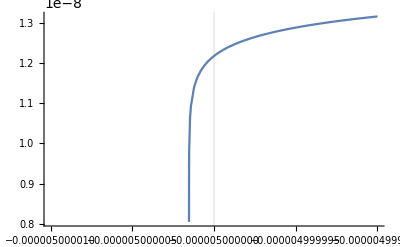

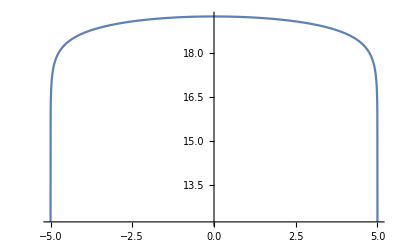

```mathematica
λ=SetPrecision[10^31,1000];
A2=10^45;
β=1;

PREC=SetPrecision[10^-50,1000];
MIN=20;

ϕ00=GetRootPhi0Max[λ,β,A2,d,MIN,PREC];

δ=SetPrecision[10^-11,1000];
Plot[ϕ[z*m2invMeV,λ,A2,β,ϕ00],{z,-0.5*10^-5-δ,-0.5*10^-5+δ},PlotRange->Full,GridLines->{{-0.5*10^-5}}]
FieldProfiles=Plot[{ϕ[z*m2invMeV*10^-6,λ,A2,β,ϕ00]*10^9},{z,-5,5},PlotRange->Full,FrameLabel->{Style["x-axis",Bold,12],Style["y-axis",Bold,12]},LabelStyle->{FontFamily->"Arial",FontSize->13},AxesLabel->{MaTeX["z[\\mu m]",Magnification->1.2],MaTeX["\\phi (z)[\\text{meV}]",Magnification->1.2]}]
```